### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={100,500,500}; (*мощности слоев*)
slopes = {0Degree, -0.9 Degree, -0.3 Degree, 2 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = 1 ;
listV = {1500,2000,2300,2500, 2800}; (*набор скоростей *)
```

```mathematica
(*folding parametres *)
hDispersion = 300;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
velocityTrend = {0,1,1,1,1};(*1 or 0*)
velocityAnomaly ={1,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
(*PlotVelocity[velModel, horizons]*)
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
```

{FittedModel[9.58468+2563.16 t],FittedModel[-81.8208+4420.24 t],FittedModel[-111.101+4589.82 t],FittedModel[530.86+2773.15 t]}

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

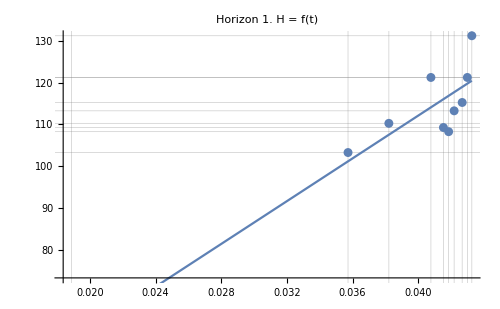
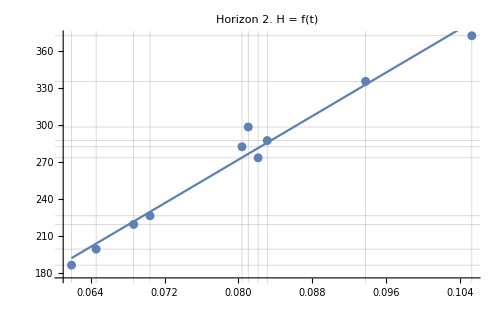
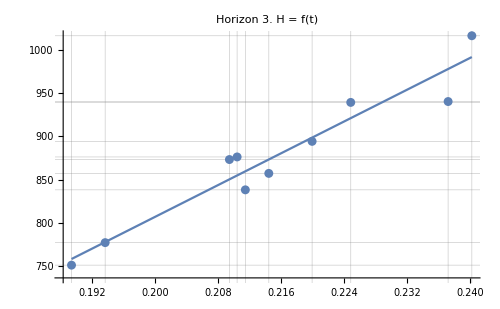
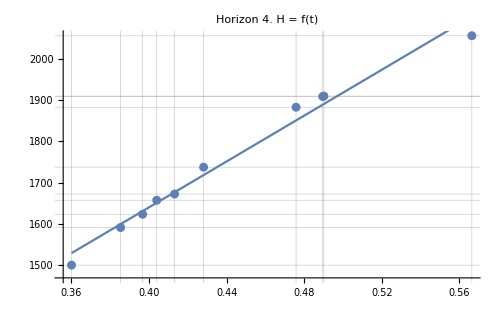

```mathematica
LinearRegressionPlots[wellValuesHT,lmSetHT, t, "H = f(t)", {"t, s","h, m"}]
```

### VTMethod

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
```

{FittedModel[3250.99-11001. t],FittedModel[2284.4+13573.6 t],FittedModel[3537.29+2478.94 t],FittedModel[5096.54-2493.11 t]}

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

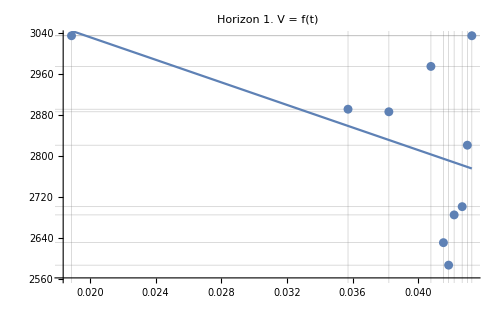
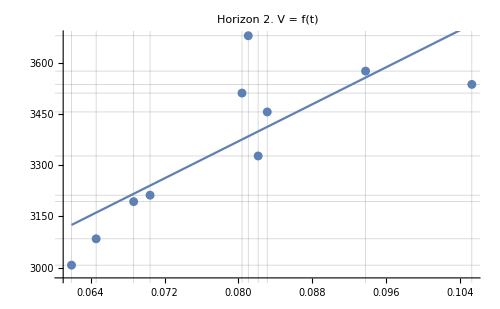
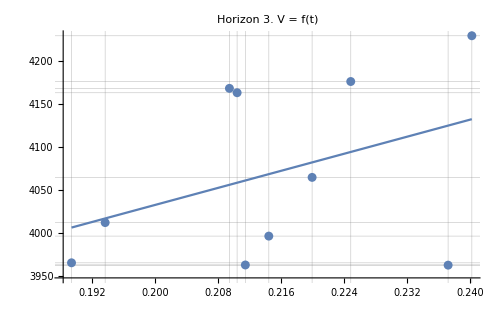
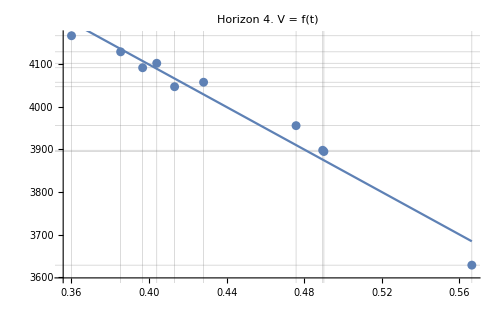

```mathematica
LinearRegressionPlots[wellValuesVT[[All, All,2;;3]],lmSetVT, t, "V = f(t)", {"t, s","v, m/s"}]
```

### THMethod

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
```

{FittedModel[0.000268593+0.000353392 h],FittedModel[0.020038+0.000220531 h],FittedModel[0.0384306+0.000201642 h],FittedModel[-0.17938+0.00035373 h]}

```mathematica
(*TimesBy[wellValuesTH[[All,All,2]],1000]
```

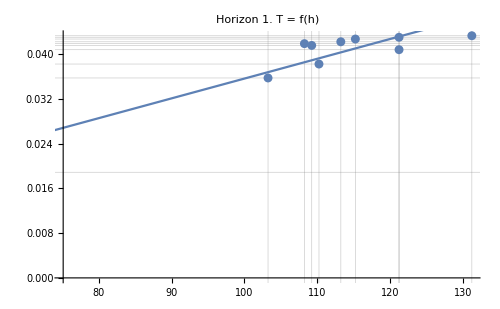
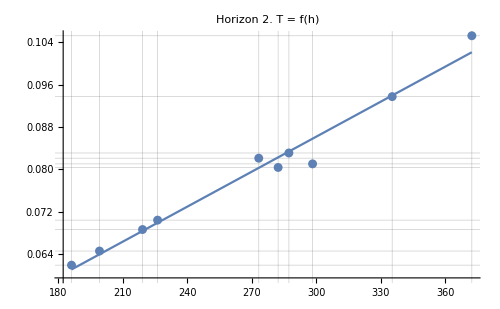
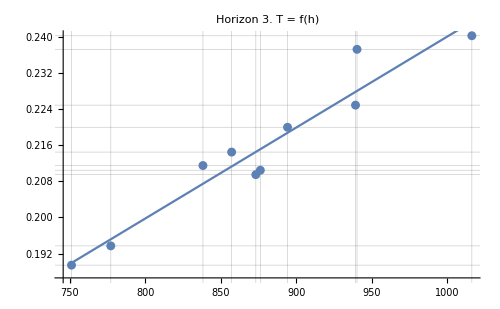
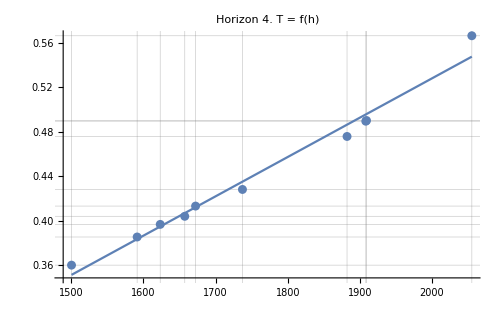

```mathematica
LinearRegressionPlots[wellValuesTH, lmSetTH, h, "T = f(h)", {"h, m","t, ms"}]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]];
```

{2824.07,3358.48,4070.61,3997.23}

### VaveVOGTMethod

```mathematica
Clear[v];
lmSetVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmSet"]]
lmParametresVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmParametres"]];
wellValuesVaveVOGT= VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["wellValues"]];
resultVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["result"]];
plotDataVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["plotData"]];
```

{FittedModel[2.44568×10^-10+1.87417 v],FittedModel[-1.22459×10^-10+0.954315 v],FittedModel[2.01325×10^-12+0.873313 v],FittedModel[-5.42167×10^-11+0.700863 v]}

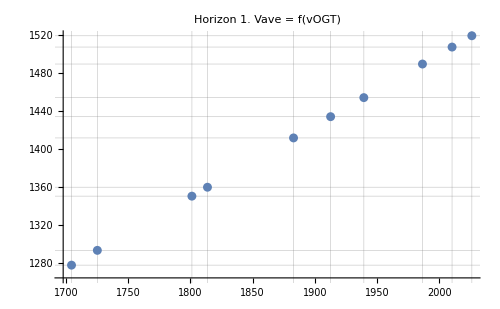
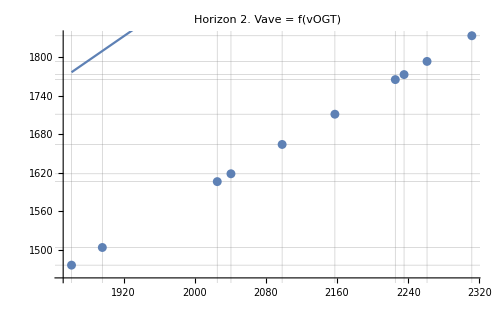
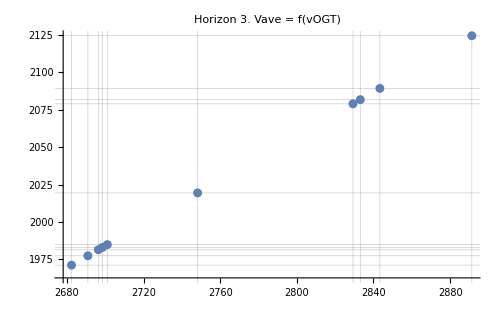
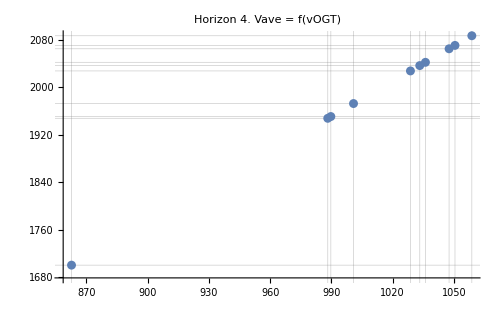

```mathematica
LinearRegressionPlots[plotDataVaveVOGT,lmSetVaveVOGT, vOGT, "Vave = f(vOGT)", {"vOGT, m/s","vAve, m/s"}]
```

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1600,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}, PlotLegends->{"H = f(t)"}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}, PlotLegends->{"V = f(t)"}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}, PlotLegends->{"T = f(h)"}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}, PlotLegends->{"Vave"}],
ListLinePlot[resultVaveVOGT[[2;;-1]], PlotStyle->{Yellow}, PlotLegends->{"Vave = f(vOGT)"}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVaveVOGT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "VaveVOGT"]
```

-Graphics-